```mathematica
ClearAll["Global`*"];
```

```mathematica
μ=0.2;Ω=0.04;d=4;rp=2.0;
V[r_]:=1-(rp/r)^(d-3);
a[r_]:=-Ω^2-μ^2*V[r]+(d-3)^2/(4*r^2)*(rp/r)^(2*(d-3));
b[r_]:=-μ^2/(r*V[r])*((d-2)-2*(rp/r)^(d-3)+(4-d)*(rp/r)^(2*(d-3)))-Ω^2/(r*V[r])*((d-2)+(2*d-7)*(rp/r)^(d-3))+(3*(d-3)^2)/(4*r^3*V[r])*(rp/r)^(2*(d-3))*((d-2)-(rp/r)^(d-3));
c[r_]:=(μ^2+Ω^2/V[r])^2+Ω^2/(4*r^2*V[r]^2)*(4*(d-2)-8*(d-2)*(rp/r)^(d-3)-(53-34*d+5*d^2)*(rp/r)^(2*(d-3)))+μ^2/(4*r^2*V[r])*(4*(d-2)-4*(3*d-7)*(rp/r)^(d-3)+(d^2+2*d-11)*(rp/r)^(2*(d-3)))+(d-3)^2/(4*r^4*V[r]^2)*(rp/r)^(2*(d-3))*((d-2)*(2*d-5)-(d-1)*(d-2)*(rp/r)^(d-3)+(rp/r)^(2*(d-3)));
```

```mathematica
crkamat={{1/2},{0,1/2},{0,0,1}};
crkbvec={1/6,1/3,1/3,1/6};
crkcvec={1/2,1/2,1};
ClassicalRungeKuttaCoefficients[4,p_]:=N[{crkamat,crkbvec,crkcvec},p];
```

```mathematica
H0=Exp[-√(Ω^2+μ^2)*200];G0=-√(Ω^2+μ^2)*H0;
r1=200.0;r2=2.001;
sol1=NDSolve[{a[r]*H''[r]+b[r]*H'[r]+c[r]*H[r]==0,H[r1]==H0,H'[r1]==G0},H[r],{r,r1,r2},Method->{"ExplicitRungeKutta","DifferenceOrder"->4,"Coefficients"->ClassicalRungeKuttaCoefficients}];
```

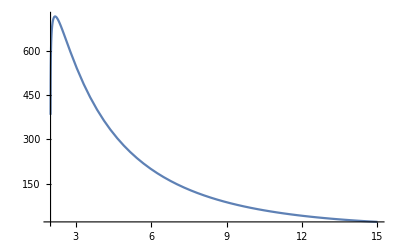

```mathematica
Htr[r_]:=H[r]/.sol1;
Plot[(r-rp)*Htr[r],{r,r2,15},PlotRange->All]
```

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
n=1;
sol2=NDSolve[{a[r]*H2''[r]+b[r]*H2'[r]+c[r]*H2[r]==0,H2[r1]==H0,H2'[r1]==G0},H2[r],{r,r1,r2},Method->{"ExplicitRungeKutta","Coefficients"->DOPRICoefficients,"DifferenceOrder"->5,"StiffnessTest"->False},StartingStepSize->0.1,AccuracyGoal->15,StepMonitor:>Print[{n,r,H2[r]}] n++];
```

{1,199.9,1.96361×10^-18}

{2,199.5,2.13113×10^-18}

{3,197.9,2.96547×10^-18}

{4,191.5,1.13278×10^-17}

{5,171.7,6.57197×10^-16}

{6,151.9,3.87332×10^-14}

{7,151.9,3.87332×10^-14}

{8,140.767,4.10312×10^-13}

{9,140.767,4.10312×10^-13}

{10,134.436,1.58152×10^-12}

{11,134.436,1.58152×10^-12}

{12,130.029,4.05244×10^-12}

{13,130.029,4.05244×10^-12}

{14,126.493,8.63188×10^-12}

{15,123.006,1.82094×10^-11}

{16,120.016,3.45708×10^-11}

{17,117.467,5.97371×10^-11}

{18,115.247,9.62621×10^-11}

{19,113.27,1.47253×10^-10}

{20,111.483,2.1633×10^-10}

{21,109.849,3.07632×10^-10}

{22,108.341,4.25836×10^-10}

{23,106.94,5.76198×10^-10}

{24,105.63,7.64579×10^-10}

{25,104.399,9.97488×10^-10}

{26,103.238,1.28212×10^-9}

{27,102.139,1.62639×10^-9}

{28,101.095,2.03899×10^-9}

{29,100.1,2.52943×10^-9}

{30,99.1496,3.10809×10^-9}

{31,98.2396,3.78629×10^-9}

{32,97.3664,4.57634×10^-9}

{33,96.5268,5.49165×10^-9}

{34,95.7179,6.54675×10^-9}

{35,94.9373,7.75746×10^-9}

{36,94.1828,9.14094×10^-9}

{37,93.4524,1.07158×10^-8}

{38,92.7441,1.25024×10^-8}

{39,92.0565,1.45225×10^-8}

{40,91.388,1.68003×10^-8}

{41,90.7373,1.93617×10^-8}

{42,90.103,2.2235×10^-8}

{43,89.484,2.54511×10^-8}

{44,88.8793,2.90438×10^-8}

{45,88.2879,3.30497×10^-8}

{46,87.7088,3.7509×10^-8}

{47,87.1412,4.24654×10^-8}

{48,86.5844,4.7967×10^-8}

{49,86.0375,5.4066×10^-8}

{50,85.4999,6.08198×10^-8}

{51,84.971,6.8291×10^-8}

{52,84.4502,7.65483×10^-8}

{53,83.9369,8.56667×10^-8}

{54,83.4307,9.57282×10^-8}

{55,82.931,1.06823×10^-7}

{56,82.4375,1.19049×10^-7}

{57,81.9497,1.32514×10^-7}

{58,81.4672,1.47335×10^-7}

{59,80.9898,1.63642×10^-7}

{60,80.517,1.81574×10^-7}

{61,80.0487,2.01285×10^-7}

{62,79.5845,2.22943×10^-7}

{63,79.1242,2.46731×10^-7}

{64,78.6675,2.72851×10^-7}

{65,78.2143,3.0152×10^-7}

{66,77.7644,3.32977×10^-7}

{67,77.3175,3.67485×10^-7}

{68,76.8735,4.05328×10^-7}

{69,76.4323,4.46818×10^-7}

{70,75.9936,4.92296×10^-7}

{71,75.5574,5.42133×10^-7}

{72,75.1235,5.96738×10^-7}

{73,74.6918,6.56554×10^-7}

{74,74.2622,7.22068×10^-7}

{75,73.8345,7.93811×10^-7}

{76,73.4087,8.72364×10^-7}

{77,72.9847,9.58362×10^-7}

{78,72.5623,1.0525×10^-6}

{79,72.1414,1.15554×10^-6}

{80,71.7221,1.26831×10^-6}

{81,71.3041,1.39172×10^-6}

{82,70.8874,1.52677×10^-6}

{83,70.472,1.67454×10^-6}

{84,70.0578,1.83621×10^-6}

{85,69.6446,2.0131×10^-6}

{86,69.2326,2.20663×10^-6}

{87,68.8215,2.41834×10^-6}

{88,68.4113,2.64994×10^-6}

{89,68.002,2.9033×10^-6}

{90,67.5936,3.18045×10^-6}

{91,67.1859,3.48361×10^-6}

{92,66.779,3.81523×10^-6}

{93,66.3729,4.17796×10^-6}

{94,65.9674,4.57471×10^-6}

{95,65.5625,5.00868×10^-6}

{96,65.1583,5.48334×10^-6}

{97,64.7547,6.00251×10^-6}

{98,64.3516,6.57036×10^-6}

{99,63.9491,7.19143×10^-6}

{100,63.5471,7.87072×10^-6}

{101,63.1457,8.61366×10^-6}

{102,62.7447,9.42623×10^-6}

{103,62.3442,0.0000103149}

{104,61.9442,0.0000112869}

{105,61.5446,0.0000123499}

{106,61.1454,0.0000135125}

{107,60.7467,0.000014784}

{108,60.3484,0.0000161746}

{109,59.9506,0.0000176954}

{110,59.5531,0.0000193587}

{111,59.1561,0.0000211776}

{112,58.7594,0.0000231669}

{113,58.3631,0.0000253423}

{114,57.9673,0.0000277215}

{115,57.5718,0.0000303233}

{116,57.1767,0.0000331686}

{117,56.782,0.0000362801}

{118,56.3877,0.0000396828}

{119,55.9938,0.0000434039}

{120,55.6002,0.0000474731}

{121,55.207,0.000051923}

{122,54.8143,0.000056789}

{123,54.4219,0.0000621102}

{124,54.0299,0.0000679289}

{125,53.6383,0.0000742917}

{126,53.2471,0.0000812494}

{127,52.8563,0.0000888575}

{128,52.4659,0.0000971767}

{129,52.0759,0.000106273}

{130,51.6863,0.00011622}

{131,51.2971,0.000127096}

{132,50.9084,0.000138989}

{133,50.52,0.000151992}

{134,50.1321,0.000166209}

{135,49.7446,0.000181755}

{136,49.3576,0.000198751}

{137,48.971,0.000217335}

{138,48.5848,0.000237653}

{139,48.1991,0.000259867}

{140,47.8138,0.000284155}

{141,47.429,0.000310708}

{142,47.0447,0.000339739}

{143,46.6609,0.000371477}

{144,46.2775,0.000406175}

{145,45.8946,0.000444107}

{146,45.5123,0.000485576}

{147,45.1304,0.00053091}

{148,44.749,0.000580468}

{149,44.3682,0.000634644}

{150,43.9879,0.000693865}

{151,43.6081,0.000758602}

{152,43.2288,0.000829366}

{153,42.8502,0.000906718}

{154,42.472,0.000991269}

{155,42.0945,0.00108369}

{156,41.7175,0.0011847}

{157,41.3411,0.00129511}

{158,40.9653,0.00141579}

{159,40.5901,0.00154768}

{160,40.2155,0.00169183}

{161,39.8415,0.00184937}

{162,39.4682,0.00202154}

{163,39.0955,0.00220971}

{164,38.7235,0.00241533}

{165,38.3522,0.00264005}

{166,37.9815,0.0028856}

{167,37.6115,0.00315393}

{168,37.2422,0.00344714}

{169,36.8737,0.00376753}

{170,36.5058,0.00411759}

{171,36.1387,0.00450008}

{172,35.7724,0.00491798}

{173,35.4068,0.00537456}

{174,35.042,0.00587338}

{175,34.678,0.00641833}

{176,34.3148,0.00701365}

{177,33.9524,0.00766397}

{178,33.5909,0.00837436}

{179,33.2302,0.00915034}

{180,32.8704,0.00999792}

{181,32.5114,0.0109237}

{182,32.1534,0.0119348}

{183,31.7963,0.013039}

{184,31.4401,0.014245}

{185,31.0848,0.0155619}

{186,30.7306,0.017}

{187,30.3773,0.0185704}

{188,30.025,0.020285}

{189,29.6738,0.0221571}

{190,29.3236,0.0242009}

{191,28.9744,0.0264323}

{192,28.6264,0.0288681}

{193,28.2794,0.0315271}

{194,27.9336,0.0344294}

{195,27.589,0.0375971}

{196,27.2455,0.0410544}

{197,26.9032,0.0448273}

{198,26.5621,0.0489445}

{199,26.2223,0.0534371}

{200,25.8837,0.0583389}

{201,25.5465,0.0636868}

{202,25.2106,0.0695209}

{203,24.876,0.075885}

{204,24.5428,0.0828267}

{205,24.2109,0.0903976}

{206,23.8806,0.0986541}

{207,23.5517,0.107658}

{208,23.2242,0.117475}

{209,22.8983,0.128178}

{210,22.574,0.139845}

{211,22.2512,0.152564}

{212,21.93,0.166426}

{213,21.6105,0.181532}

{214,21.2927,0.197994}

{215,20.9766,0.215929}

{216,20.6622,0.235468}

{217,20.3496,0.256752}

{218,20.0389,0.279932}

{219,19.73,0.305176}

{220,19.4229,0.332662}

{221,19.1179,0.362586}

{222,18.8148,0.395158}

{223,18.5137,0.430609}

{224,18.2146,0.469187}

{225,17.9176,0.51116}

{226,17.6228,0.55682}

{227,17.3301,0.606481}

{228,17.0397,0.660486}

{229,16.7515,0.719204}

{230,16.4656,0.783033}

{231,16.182,0.852405}

{232,15.9008,0.927786}

{233,15.6221,1.00968}

{234,15.3458,1.09863}

{235,15.072,1.19523}

{236,14.8008,1.30011}

{237,14.5321,1.41394}

{238,14.2661,1.53748}

{239,14.0028,1.67151}

{240,13.7422,1.81688}

{241,13.4844,1.97453}

{242,13.2294,2.14543}

{243,12.9772,2.33066}

{244,12.7279,2.53137}

{245,12.4816,2.74877}

{246,12.2382,2.9842}

{247,11.9978,3.23909}

{248,11.7605,3.51494}

{249,11.5262,3.81341}

{250,11.2951,4.13623}

{251,11.0671,4.4853}

{252,10.8423,4.86263}

{253,10.6207,5.27037}

{254,10.4023,5.71083}

{255,10.1872,6.18648}

{256,9.97542,6.69996}

{257,9.76693,7.25408}

{258,9.56178,7.85186}

{259,9.35997,8.49651}

{260,9.16155,9.19147}

{261,8.9665,9.9404}

{262,8.77485,10.7472}

{263,8.58661,11.616}

{264,8.40179,12.5513}

{265,8.22038,13.5578}

{266,8.0424,14.6405}

{267,7.86783,15.8047}

{268,7.69669,17.0562}

{269,7.52896,18.401}

{270,7.36463,19.8455}

{271,7.2037,21.3966}

{272,7.04615,23.0615}

{273,6.89197,24.8479}

{274,6.74114,26.764}

{275,6.59363,28.8185}

{276,6.44944,31.0207}

{277,6.30852,33.3802}

{278,6.17086,35.9075}

{279,6.03643,38.6136}

{280,5.90519,41.5101}

{281,5.77712,44.6095}

{282,5.65217,47.9249}

{283,5.53031,51.4701}

{284,5.41151,55.26}

{285,5.29571,59.3103}

{286,5.18289,63.6376}

{287,5.07299,68.2595}

{288,4.96598,73.1948}

{289,4.86179,78.4636}

{290,4.7604,84.087}

{291,4.66174,90.0876}

{292,4.56578,96.4896}

{293,4.47244,103.319}

{294,4.3817,110.603}

{295,4.29347,118.371}

{296,4.20772,126.656}

{297,4.12439,135.491}

{298,4.0434,144.915}

{299,3.96471,154.967}

{300,3.88824,165.693}

{301,3.81393,177.143}

{302,3.7417,189.371}

{303,3.67148,202.44}

{304,3.60317,216.421}

{305,3.53669,231.395}

{306,3.47196,247.456}

{307,3.40892,264.696}

{308,3.34766,283.18}

{309,3.28869,302.814}

{310,3.23343,323.093}

{311,3.1837,343.115}

{312,3.14022,362.175}

{313,3.10258,379.984}

{314,3.07005,396.46}

{315,3.04194,411.585}

{316,3.01766,425.364}

{317,2.99672,437.817}

{318,2.97872,448.972}

{319,2.96332,458.868}

{320,2.95022,467.551}

{321,2.93917,475.072}

{322,2.93917,475.072}

{323,2.93161,480.326}

{324,2.92405,485.67}

{325,2.92405,485.67}

{326,2.91902,489.275}

{327,2.91902,489.275}

{328,2.91489,492.264}

{329,2.91489,492.264}

{330,2.91166,494.628}

{331,2.91166,494.628}

{332,2.90918,496.447}

{333,2.90918,496.447}

{334,2.90738,497.781}

{335,2.90738,497.781}

{336,2.90613,498.704}

{337,2.90613,498.704}

{338,2.90534,499.296}

{339,2.90534,499.296}

{340,2.90486,499.648}

{341,2.90486,499.648}

{342,2.9046,499.842}

{343,2.9046,499.842}

{344,2.90445,499.952}

{345,2.90445,499.952}

{346,2.90438,500.011}

{347,2.9043,500.07}

{348,2.90422,500.128}

{349,2.90399,500.301}

{350,2.9035,500.664}

{351,2.90266,501.294}

{352,2.90136,502.269}

{353,2.89951,503.66}

{354,2.89703,505.536}

{355,2.89384,507.961}

{356,2.88988,510.999}

{357,2.8851,514.708}

{358,2.87944,519.148}

{359,2.87288,524.373}

{360,2.86539,530.44}

{361,2.85695,537.401}

{362,2.84757,545.308}

{363,2.83726,554.212}

{364,2.82604,564.161}

{365,2.81395,575.203}

{366,2.80102,587.38}

{367,2.78732,600.735}

{368,2.77291,615.307}

{369,2.75786,631.132}

{370,2.74224,648.243}

{371,2.72613,666.672}

{372,2.70961,686.447}

{373,2.69277,707.595}

{374,2.67568,730.143}

{375,2.65841,754.115}

{376,2.64104,779.536}

{377,2.62364,806.432}

{378,2.60626,834.829}

{379,2.58895,864.755}

{380,2.57178,896.24}

{381,2.55477,929.316}

{382,2.53797,964.015}

{383,2.52141,1000.37}

{384,2.50512,1038.43}

{385,2.48912,1078.23}

{386,2.47343,1119.81}

{387,2.45806,1163.23}

{388,2.44303,1208.52}

{389,2.42835,1255.75}

{390,2.41402,1304.97}

{391,2.40005,1356.23}

{392,2.38645,1409.59}

{393,2.37321,1465.13}

{394,2.36033,1522.9}

{395,2.34782,1582.98}

{396,2.33566,1645.43}

{397,2.32387,1710.34}

{398,2.31242,1777.78}

{399,2.30132,1847.84}

{400,2.29057,1920.59}

{401,2.28015,1996.13}

{402,2.27006,2074.54}

{403,2.2603,2155.93}

{404,2.25085,2240.39}

{405,2.24171,2328.03}

{406,2.23287,2418.95}

{407,2.22433,2513.26}

{408,2.21607,2611.08}

{409,2.2081,2712.52}

{410,2.20039,2817.71}

{411,2.19295,2926.78}

{412,2.18577,3039.85}

{413,2.17884,3157.07}

{414,2.17215,3278.58}

{415,2.1657,3404.53}

{416,2.15947,3535.06}

{417,2.15347,3670.33}

{418,2.14768,3810.52}

{419,2.1421,3955.78}

{420,2.13671,4106.3}

{421,2.13153,4262.26}

{422,2.12653,4423.84}

{423,2.12171,4591.23}

{424,2.11707,4764.65}

{425,2.1126,4944.3}

{426,2.1083,5130.4}

{427,2.10415,5323.16}

{428,2.10016,5522.83}

{429,2.09631,5729.64}

{430,2.09261,5943.84}

{431,2.08904,6165.69}

{432,2.08561,6395.46}

{433,2.08231,6633.41}

{434,2.07913,6879.84}

{435,2.07607,7135.04}

{436,2.07313,7399.31}

{437,2.0703,7672.98}

{438,2.06757,7956.36}

{439,2.06495,8249.8}

{440,2.06243,8553.65}

{441,2.06,8868.26}

{442,2.05767,9194.02}

{443,2.05542,9531.31}

{444,2.05326,9880.53}

{445,2.05118,10242.1}

{446,2.04919,10616.4}

{447,2.04726,11004.}

{448,2.04542,11405.2}

{449,2.04364,11820.6}

{450,2.04193,12250.7}

{451,2.04029,12695.9}

{452,2.03871,13156.7}

{453,2.0372,13633.8}

{454,2.03574,14127.7}

{455,2.03433,14638.9}

{456,2.03299,15168.1}

{457,2.03169,15715.8}

{458,2.03044,16282.8}

{459,2.02925,16869.7}

{460,2.0281,17477.2}

{461,2.02699,18105.9}

{462,2.02593,18756.7}

{463,2.0249,19430.2}

{464,2.02392,20127.3}

{465,2.02298,20848.7}

{466,2.02207,21595.4}

{467,2.0212,22368.1}

{468,2.02036,23167.8}

{469,2.01956,23995.4}

{470,2.01878,24851.8}

{471,2.01804,25738.}

{472,2.01733,26655.1}

{473,2.01664,27604.1}

{474,2.01598,28586.1}

{475,2.01535,29602.1}

{476,2.01474,30653.5}

{477,2.01416,31741.3}

{478,2.0136,32866.9}

{479,2.01306,34031.4}

{480,2.01254,35236.3}

{481,2.01204,36482.9}

{482,2.01156,37772.5}

{483,2.0111,39106.7}

{484,2.01066,40487.}

{485,2.01024,41914.8}

{486,2.00983,43391.9}

{487,2.00944,44919.9}

{488,2.00906,46500.4}

{489,2.0087,48135.3}

{490,2.00835,49826.4}

{491,2.00802,51575.5}

{492,2.0077,53384.6}

{493,2.00739,55255.7}

{494,2.0071,57191.}

{495,2.00682,59192.4}

{496,2.00654,61262.2}

{497,2.00628,63402.7}

{498,2.00603,65616.3}

{499,2.00579,67905.3}

{500,2.00556,70272.3}

{501,2.00534,72719.8}

{502,2.00512,75250.5}

{503,2.00492,77867.1}

{504,2.00472,80572.5}

{505,2.00453,83369.6}

{506,2.00435,86261.4}

{507,2.00417,89251.}

{508,2.00401,92341.5}

{509,2.00385,95536.4}

{510,2.00369,98838.9}

{511,2.00354,102253.}

{512,2.0034,105781.}

{513,2.00326,109428.}

{514,2.00313,113197.}

{515,2.00301,117093.}

{516,2.00289,121119.}

{517,2.00277,125280.}

{518,2.00266,129579.}

{519,2.00255,134022.}

{520,2.00245,138613.}

{521,2.00235,143356.}

{522,2.00225,148257.}

{523,2.00216,153320.}

{524,2.00208,158551.}

{525,2.00199,163955.}

{526,2.00191,169537.}

{527,2.00183,175304.}

{528,2.00176,181260.}

{529,2.00169,187411.}

{530,2.00162,193765.}

{531,2.00155,200326.}

{532,2.00149,207102.}

{533,2.00143,214099.}

{534,2.00137,221324.}

{535,2.00132,228784.}

{536,2.00126,236487.}

{537,2.00121,244439.}

{538,2.00116,252648.}

{539,2.00111,261122.}

{540,2.00107,269869.}

{541,2.00103,276871.}

{542,2.001,284288.}

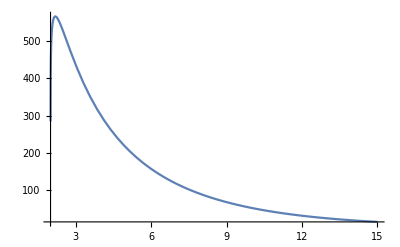

```mathematica
Htr2[r_]:=H2[r]/.sol2;
Gtr2[r_]:=H2'[r]/.sol2;
Plot[{(r-rp)*Htr2[r]},{r,r2,15},PlotRange->All]
```